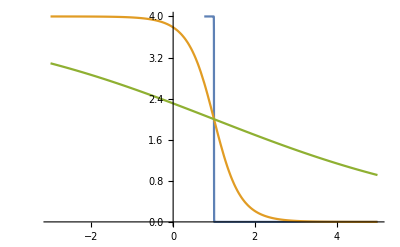

```mathematica
k = 8.617*10^-5
μ = 1

ftwo[T_]:=2*(Exp[(-(ϵ-μ))/(k*T)] + 2*Exp[-2*(ϵ-μ)/(k*T)])/(1 + Exp[(-(ϵ-μ))/(k*T)] + Exp[-2*(ϵ-μ)/(k*T)])

Plot[{ftwo[10], ftwo[5000], ftwo[50000]}, {ϵ, -3, 5}, PlotRange-> All]
```